```mathematica
Clear[Ε,V,B,q,ω,m,ν,c,L,v,u,Eps,Ι];
-ⅈ*ω*m*V==q*(Ε+V×B)-ν*m*V;(*ω->ω+ⅈν=ω(1+ⅈα/2) - учтем только в первом порядке*)
V==q*Inverse[{{-ⅈ*m*ω+ν*m,-B*q/c,0},{B*q/c,-ⅈ*m*ω+ν*m,0},{0,0,-ⅈ*m*ω+ν*m}}].Ε;
Ι={{1,0,0},{0,1,0},{0,0,1}};
Eps=FullSimplify[Ι+ⅈ*4*π/ω*q^2*n[x]*Inverse[{{-ⅈ*m*ω+ν*m,-B*q/c,0},{B*q/c,-ⅈ*m*ω+ν*m,0},{0,0,-ⅈ*m*ω+ν*m}}]];
MatrixForm[Eps]
(*p^2=4πe^2*n/m b=eB/(mc) v=p^2/ω^2 u=b^2/ω^2, учет ν: v->v(1-ⅈα)*)
Eps={{1-v[x]/(1-u),ⅈ*v[x](1-ⅈ*α)*Sqrt[u]/(1-u),0},{-ⅈ*v[x]*Sqrt[u]/(1-u),1-v[x]/(1-u),0},{0,0,1-v[x]}}/.{v[x]->v[x](1-ⅈ*α),u->u(1-ⅈ*α)};
Δ=Eps[[1]][[1]]Eps[[2]][[2]]-Eps[[1]][[2]]Eps[[2]][[1]];
MatrixForm[Eps]
```

(1+(4 c^2 m π q^2 (ⅈ ν+ω) n[x])/((B^2 q^2+c^2 m^2 (ν-ⅈ ω)^2) ω) | (4 ⅈ B c π q^3 n[x])/((B^2 q^2+c^2 m^2 (ν-ⅈ ω)^2) ω) | 0
-(4 ⅈ B c π q^3 n[x])/((B^2 q^2+c^2 m^2 (ν-ⅈ ω)^2) ω) | 1+(4 c^2 m π q^2 (ⅈ ν+ω) n[x])/((B^2 q^2+c^2 m^2 (ν-ⅈ ω)^2) ω) | 0
0 | 0 | 1+(4 ⅈ π q^2 n[x])/(m ν ω-ⅈ m ω^2))

(1-((1-ⅈ α) v[x])/(1-u (1-ⅈ α)) | (ⅈ (1-ⅈ α)^2 √(u (1-ⅈ α)) v[x])/(1-u (1-ⅈ α)) | 0
-(ⅈ (1-ⅈ α) √(u (1-ⅈ α)) v[x])/(1-u (1-ⅈ α)) | 1-((1-ⅈ α) v[x])/(1-u (1-ⅈ α)) | 0
0 | 0 | 1-(1-ⅈ α) v[x])

```mathematica
A1*B''[x]+A2*B'[x]+A3*B[x]==0;
(*χ==k0*L, x->x/L*)
(*Считая, что вблизи точки отражения v[x]=a(1+x/L)=x, запишем:*)
v=Function[x,1+x];
A1=FullSimplify[Δ*Eps[[1]][[1]]^2];
A2=FullSimplify[Eps[[1]][[1]]*(Δ*D[Eps[[1]][[1]],x]-Eps[[1]][[1]]D[Δ,x])];
A3=FullSimplify[Δ^2*χ^2(Eps[[1]][[1]]-Sin[θ]^2)-Δ*χ^2*Sin[θ]^2*Eps[[1]][[2]]Eps[[2]][[1]]+ⅈ*χ*Sin[θ]*Eps[[1]][[1]](Δ*D[Eps[[2]][[1]],x]-Eps[[2]][[1]]D[Δ,x])];
```

```mathematica
FullSimplify[Series[A1,{x,0,1},{α,0,2}]]
FullSimplify[Series[A2,{x,0,1},{α,0,1}]]
FullSimplify[Series[A3,{x,0,1},{α,0,1}]]
```

((u α^2)/(-1+u)^2+O[α]^3)+((2 ⅈ u α)/(-1+u)^2+(2 (-6+u) u α^2)/(-1+u)^3+O[α]^3) x+O[x]^2

((ⅈ u α)/(-1+u)^2+O[α]^2)+(-u/(-1+u)^2+(2 ⅈ (-2+u) u α)/(-1+u)^3+O[α]^2) x+O[x]^2

(-(ⅈ χ ((-1+u) u^2 χ-u^(3/2) Sin[θ]) α)/(-1+u)^2+O[α]^2)+((χ ((-1+u) u^2 χ-u^(3/2) Sin[θ]))/(-1+u)^2-(ⅈ χ (2 (-1+u) u^2 (-13+4 u) χ+√u (-8+(17-5 u) u) Sin[θ]+4 (-1+u) u χ Sin[θ]^2) α)/(2 (-1+u)^3)+O[α]^2) x+O[x]^2

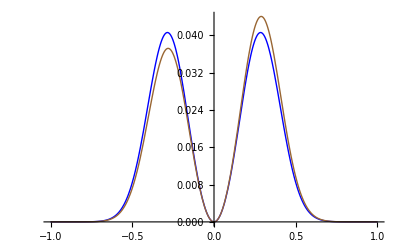

```mathematica
Plot[{Sin[θ]^2*Exp[-30*Abs[Sin[θ]^3]],(1+0.3*Sin[θ])Sin[θ]^2*Exp[-30*Abs[Sin[θ]^3]]},{θ,-1,1},PlotStyle->{Blue,Brown}]
```

```mathematica
σ={{α+ⅈ,Sqrt[u],0},{-Sqrt[u],α+ⅈ,0},{0,0,α+ⅈ}};
E0={1/(x-ⅈ*α),ⅈ*χ*Sin[θ]*Log[x-ⅈ*α],0};
E1=Sqrt[u]*χ^2*(x-ⅈ*α)*Log[x-ⅈ*α]{χ(x-ⅈ*α)/(3*Sin[θ]),ⅈ,0};
Q=(σ.(E0+E1)).({1/(x+ⅈ*α),-ⅈ*χ*Sin[θ]*Log[x+ⅈ*α],0}+Sqrt[u]*χ^2*(x+ⅈ*α)*Log[x+ⅈ*α]{χ(x+ⅈ*α)/(3*Sin[θ]),-ⅈ,0})
```

(1/(x+ⅈ α)+1/3 √u (x+ⅈ α)^2 χ^3 Csc[θ] Log[x+ⅈ α]) ((ⅈ+α) (1/(x-ⅈ α)+1/3 √u (x-ⅈ α)^2 χ^3 Csc[θ] Log[x-ⅈ α])+√u (ⅈ √u (x-ⅈ α) χ^2 Log[x-ⅈ α]+ⅈ χ Log[x-ⅈ α] Sin[θ]))+(-ⅈ √u (x+ⅈ α) χ^2 Log[x+ⅈ α]-ⅈ χ Log[x+ⅈ α] Sin[θ]) (-√u (1/(x-ⅈ α)+1/3 √u (x-ⅈ α)^2 χ^3 Csc[θ] Log[x-ⅈ α])+(ⅈ+α) (ⅈ √u (x-ⅈ α) χ^2 Log[x-ⅈ α]+ⅈ χ Log[x-ⅈ α] Sin[θ]))

```mathematica
FullSimplify[Series[Q,{u,0,1}]]
```

(ⅈ+α) (1/(x^2+α^2)+χ^2 Log[x-ⅈ α] Log[x+ⅈ α] Sin[θ]^2)+(χ ((ⅈ+α) χ^2 Csc[θ] ((x-ⅈ α)^3 Log[x-ⅈ α]+(x+ⅈ α)^3 Log[x+ⅈ α])+3 (ⅈ (x+ⅈ α) Log[x+ⅈ α]+Log[x-ⅈ α] (ⅈ x+α+2 x (ⅈ+α) (x^2+α^2) χ^2 Log[x+ⅈ α])) Sin[θ]) √u)/(3 (x^2+α^2))+(χ^2 (9 ⅈ (x+ⅈ α)^2 Log[x+ⅈ α]+(ⅈ+α) (x^2+α^2)^3 χ^4 Csc[θ]^2 Log[x-ⅈ α] Log[x+ⅈ α]+3 (x-ⅈ α) Log[x-ⅈ α] (3 (ⅈ x+α)+(x+ⅈ α) (α^2 (ⅈ+3 α)+x^2 (5 ⅈ+3 α)) χ^2 Log[x+ⅈ α])) u)/(9 (x^2+α^2))+O[u]^(3/2)

```mathematica
α/(x^2+α^2)+(χ (α* χ^2 Csc[θ] 2Re[(x-ⅈ α)^3 Log[x-ⅈ α]]+3 2Re[(ⅈ x- α) Log[x+ⅈ α]]Sin[θ]) √u)/(3 (x^2+α^2))
```

```mathematica
Eps={{-x+ⅈ*α,ⅈ*Sqrt[u],0},{-ⅈ*Sqrt[u],-x+ⅈ*α,0},{0,0,-x+ⅈ*α}};
Δ=Eps[[1]][[1]]Eps[[2]][[2]]-Eps[[1]][[2]]Eps[[2]][[1]];
A1=FullSimplify[Δ*Eps[[1]][[1]]^2];
A2=FullSimplify[Eps[[1]][[1]]*(Δ*D[Eps[[1]][[1]],x]-Eps[[1]][[1]]D[Δ,x])];
A3=FullSimplify[Δ^2*χ^2(Eps[[1]][[1]]-Sin[θ]^2)-Δ*χ^2*Sin[θ]^2*Eps[[1]][[2]]Eps[[2]][[1]]+ⅈ*χ*Sin[θ]*Eps[[1]][[1]](Δ*D[Eps[[2]][[1]],x]-Eps[[2]][[1]]D[Δ,x])];
```

```mathematica
FullSimplify[A2/A1/.α->0]
FullSimplify[A3/A1/.α->0]
```

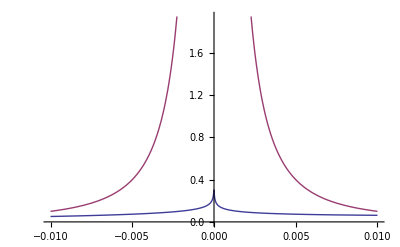

```mathematica
Plot[{Re[Q-α/(x^2+α^2)/.{α->0.00001,χ->30,θ->π/6,u->0.1}],((α/(x^2+α^2))/.{α->0.00001,χ->30,θ->π/6,u->0.1})},{x,-0.01,0.01}]
```

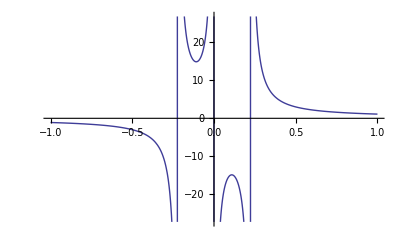

```mathematica
Plot[(x^2+u)/(x(x^2-u))/.u->0.05,{x,-1,1},PlotRange->Automatic]
```

```mathematica
Integrate[(1-x^2)/x,x]
```

-x^2/2+Log[x]

```mathematica
NDSolve[{y''[x]+(0.001/x-x)y[x]==0,y[1]==1,y'[1]==0},y[x],{x,-2,2}]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == 1.17482984132913×10^-589.

{{y[x]→InterpolatingFunction[{{1.17482984132913×10^-589,2.}},<>][x]}}

```mathematica
DSolve[y''[x]-y'[x]/x-α*y[x]/x==0,y[x],x]
```

{{y[x]→2 x α BesselI[2,2 √x √α] C[1]+2 x α BesselK[2,2 √x √α] C[2]}}

```mathematica
Series[x(Am*BesselJ[2,2ⅈ*Sqrt[x*χ*Sin[θ]]]+Bm*BesselY[2,2ⅈ*Sqrt[x*χ*Sin[θ]]]),{x,0,1}]
```

((Bm Csc[θ])/(π χ)+O[x]^1)+Floor[(π-Arg[x]/2-Arg[(ⅈ √(x χ Sin[θ]))/(√x)])/(2 π)] (-2 ⅈ Bm χ Sin[θ] x^2+O[x]^3)+Floor[Arg[-(ⅈ (√x √(χ Sin[θ])-√(x χ Sin[θ])))/(√x)]/(2 π)] (-(Bm χ Log[-ⅈ/(√(χ Sin[θ]))] Sin[θ] x^2)/π+O[x]^3)+Floor[Arg[-(ⅈ (√x √(χ Sin[θ])-√(x χ Sin[θ])))/(√x)]/(2 π)] (-(Bm χ Log[ⅈ √(χ Sin[θ])] Sin[θ] x^2)/π+O[x]^3)+(-1/2 (Am χ Sin[θ]) x^2+O[x]^(5/2)) (-ⅈ/(√(χ Sin[θ])))^(2 Floor[Arg[-(ⅈ (√x √(χ Sin[θ])-√(x χ Sin[θ])))/(√x)]/(2 π)]) (ⅈ √(χ Sin[θ]))^(2 Floor[Arg[-(ⅈ (√x √(χ Sin[θ])-√(x χ Sin[θ])))/(√x)]/(2 π)])

```mathematica
Ey=((ⅈ*χ*Exx[x]*Exy[x]-Sin[θ]*Exx'[x])Ex[x]-Sin[θ]*Exx[x]*Ex'[x])/(ⅈ*χ(Sin[θ]^2*Eyy[x]-Exy[x]^2)+Sin[θ]*Exy'[x]);
eq=Sin[θ]*D[Ey,x]-ⅈ*χ*(Sin[θ]^2*Ex[x]-(Exx[x]*Ex[x]+Exy[x]*Ey));
FullSimplify[eq/.{Exx[x]->-x,Exx'[x]->-1,Exx''[x]->0,Exy[x]->ⅈ*√u,Exy'[x]->0,Exy''[x]->0,Eyx[x]->-ⅈ*√u,Eyx'[x]->0,Eyy[x]->-x,Eyy'[x]->-1}]
```

-(ⅈ Sin[θ]^2 (Ex[x] (u (u-x^2) χ^2+√u x χ Sin[θ]+(1+x (-2 u+x^2) χ^2) Sin[θ]^2+x^2 χ^2 Sin[θ]^4)+(2 u-x Sin[θ]^2) Ex'[x]+x (u-x Sin[θ]^2) Ex''[x]))/(χ (u-x Sin[θ]^2)^2)

```mathematica
(Ex[x] (u (u-x^2) χ^2+√u x χ Sin[θ]+(1+x (-2 u+x^2) χ^2) Sin[θ]^2+x^2 χ^2 Sin[θ]^4)+(2 u-x Sin[θ]^2) Ex'[x]+x (u-x Sin[θ]^2) Ex''[x])/.u->0
```

Ex[x] ((1+x^3 χ^2) Sin[θ]^2+x^2 χ^2 Sin[θ]^4)-x Sin[θ]^2 Ex'[x]-x^2 Sin[θ]^2 Ex''[x]

```mathematica
eq1=Ey'[x]
```